## Exclusion Plots, Run ~/Dropbox/nEDM/NStar/mNStar/mBpSens_2012.nb

## Initialize

```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
taue[bp_,b_,m_]:=m/8 Sqrt[(3b^2-bp^2)b^2/(b^2-bp^2)^2]
taubca[bp_,b_,m_]:=m /8Sqrt[b^2(bp^3)/(b(b^2-bp^2)^2)]
tauold[bp_,bb_,m_]:=m √((bb^2 (bb^2+bp^2+(2bp bb)))/((bp^2-bb^2)^2))
(**OLD**)
taubppnpi[bb_,bp_,tso_,beta_,nco_,tfoil_]:=((hc×8×(1.4275×10^6)*nco)/(mun*32))√(2/tfoil*(√(32/(nnn[tso]×nco)))^-1*(bb^2+bp^2+(2bp bb Cos[beta]))/((bp^2-bb^2)^2));
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
taue[0,bb,m]
taubca[0,bb,m]
tauold[0,bb,m]
```

(√3 m)/4

0

m

## Ratios

```mathematica
a10=e10=a20=e20={};
b10=b20={};
tstf10=tstf20={};
tstf102=tstf202={};
tsadd=PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
If[(*!MemberQ[{6,7,8,9,10,11,12,13,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]*)(descdat[[i]][[5]]>100&&descdat[[i]][[5]]<900),
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
If[descdat[[i]][[6]]==10,
a10=AppendTo[a10,PlusMinus[lvl3[[1]][[1]],lvl3[[1]][[2]]]];
e10=AppendTo[e10,PlusMinus[lvl3[[1]][[3]],lvl3[[1]][[4]]]];
b10=AppendTo[b10,PlusMinus[lvl3[[1]][[7]],lvl3[[1]][[8]]]];
tstf10=AppendTo[tstf10,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
tstf102=AppendTo[tstf102,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)*PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];,
a20=AppendTo[a20,PlusMinus[lvl3[[1]][[1]],lvl3[[1]][[2]]]];
e20=AppendTo[e20,PlusMinus[lvl3[[1]][[3]],lvl3[[1]][[4]]]];
b20=AppendTo[b20,PlusMinus[lvl3[[1]][[7]],lvl3[[1]][[8]]]];
tstf20=AppendTo[tstf20,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
tstf202=AppendTo[tstf202,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)*PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
];
];
]
Print["<A_10> = ",Mean[a10]]
Quiet[Print["<A_10> 99% = ",a1099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 95% = ",a1095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 90% = ",a1090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<E_10> = ",Mean[e10]]
Quiet[Print["<E_10> 99% = ",e1099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_10> 95% = ",e1095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_10> 90% = ",e1090=
(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==
0.1Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<B_10> = ",Mean[b10]]
(***)
Print["<A_20> = ",Mean[a20]]
Quiet[Print["<A_20> 99% = ",a2099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_20> 95% = ",a2095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 90% = ",a2090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<E_20> = ",Mean[e20]]
Quiet[Print["<E_20> 99% = ",e2099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_20> 95% = ",e2095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_20> 90% = ",e2090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<B_20> = ",Mean[b20]]
Print["E_B0 < 99% = ",b0e99=1/Sqrt[(1/e1099)^2+(1/e2099)^2]]
Print["E_B0 < 95% = ",b0e95=1/Sqrt[(1/e1095)^2+(1/e2095)^2]]
Print["E_B0 < 90% = ",b0e90=1/Sqrt[(1/e1090)^2+(1/e2090)^2]]
Sqrt[400*.09/b0e90]
```

<A_10> = 0.0002±0.00028

<A_10> 99% = -0.000590575

<A_10> 95% = -0.00043311

<A_10> 90% = -0.000354895

<E_10> = 0.±0.0004

<E_10> 99% = -0.000895427

<E_10> 95% = -0.000663582

<E_10> 90% = -0.000547357

<B_10> = 0.0101954±1.5×10^-6

<A_20> = 0.0001±0.0004

<A_20> 99% = -0.000960392

<A_20> 95% = -0.000720966

<A_10> 90% = -0.000599675

<E_20> = 0.00043±0.00053

<E_20> 99% = -0.00108838

<E_20> 95% = -0.000794579

<E_20> 90% = -0.00064925

<B_20> = 0.0203867±1.×10^-7

E_B0 < 99% = 0.000691483

E_B0 < 95% = 0.000509325

E_B0 < 90% = 0.000418482

293.3

## B,(E-1)

```mathematica
gamman90=2Pi  (29.1646943-1.64 0.0000069)*0.001;
gamman95=2Pi (29.1646943-1.96 0.0000069)*0.001;
gamman99=2Pi (29.1646943-2.58 0.0000069)*0.001;
dim10=Dimensions[e10][[1]];
dim20=Dimensions[e20][[1]];
taue1090=taue1095=taue1099={};
taue2090=taue2095=taue2099={};
tauo1090=tauo1095=tauo1099={};
tauo2090=tauo2095=tauo2099={};
taua1090=taua1095=taua1099={};
taua2090=taua2095=taua2099={};
For[i=1,i≤dim10,i++,
(*90*)
taue1090=
AppendTo[taue1090,Sqrt[(tstf10[[i]][[1]]*gamman90^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taue1095=
AppendTo[taue1095,Sqrt[(tstf10[[i]][[1]]*gamman95^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taue1099=
AppendTo[taue1099,Sqrt[(tstf10[[i]][[1]]*gamman99^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
taue2090=AppendTo[taue2090,Sqrt[(tstf20[[i]][[1]]*gamman90^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taue2095=
AppendTo[taue2095,Sqrt[(tstf20[[i]][[1]]*gamman95^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taue2099=
AppendTo[taue2099,Sqrt[(tstf20[[i]][[1]]*gamman99^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(***A***)
dim10=Dimensions[a10][[1]];
dim20=Dimensions[a20][[1]];
For[i=1,i≤dim10,i++,
(*90*)
taua1090=
AppendTo[taua1090,Sqrt[(tstf10[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taua1095=
AppendTo[taua1095,Sqrt[(tstf10[[i]][[1]]*gamman95^2)/(2*Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taua1099=
AppendTo[taua1099,Sqrt[(tstf10[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
taua2090=AppendTo[taua2090,Sqrt[(tstf20[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taua2095=
AppendTo[taua2095,Sqrt[(tstf20[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taua2099=
AppendTo[taua2099,Sqrt[(tstf20[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(***O***)
dim10=Dimensions[e10][[1]];
dim20=Dimensions[e20][[1]];
For[i=1,i≤dim10,i++,
(*90*)
tauo1090=
AppendTo[tauo1090,Sqrt[(tstf102[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
tauo1095=
AppendTo[tauo1095,Sqrt[(tstf102[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
tauo1099=
AppendTo[tauo1099,Sqrt[(tstf102[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
tauo2090=AppendTo[tauo2090,Sqrt[(tstf202[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
tauo2095=
AppendTo[tauo2095,Sqrt[(tstf202[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
tauo2099=
AppendTo[tauo2099,Sqrt[(tstf202[[i]][[1]])/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
me1090=(Total[taue1090^4])^.25;Mean[taue1090]-1.64StandardDeviation[taue1090] ;
me1095=(Total[taue1095^4])^.25;Mean[taue1095]-1.96 StandardDeviation[taue1095]; 
me1099=(Total[taue1099^4])^.25;Mean[taue1099]-2.58 StandardDeviation[taue1099] ;
me2090=(Total[taue2090^4])^.25;Mean[taue2090]-1.64StandardDeviation[taue2090] ;
me2095=(Total[taue2095^4])^.25;Mean[taue2095]-1.96 StandardDeviation[taue2095] ;
me2099=(Total[taue2099^4])^.25;Mean[taue2099]-2.58 StandardDeviation[taue2099] ;
(*o*)
mo1090=(Total[tauo1090^4])^.25;Mean[tauo1090]-1.64StandardDeviation[tauo1090] ;
mo1095=(Total[tauo1095^4])^.25;Mean[tauo1095]-1.96 StandardDeviation[tauo1095]; 
mo1099=(Total[tauo1099^4])^.25;Mean[tauo1099]-2.58 StandardDeviation[tauo1099] ;
mo2090=(Total[tauo2090^4])^.25;Mean[tauo2090]-1.64StandardDeviation[tauo2090] ;
mo2095=(Total[tauo2095^4])^.25;Mean[tauo2095]-1.96 StandardDeviation[tauo2095] ;
mo2099=(Total[tauo2099^4])^.25;Mean[tauo2099]-2.58 StandardDeviation[tauo2099] ;
(*e*)
ma1090=(Total[taua1090^4])^.25;Mean[taua1090]-1.64StandardDeviation[taua1090] ;
ma1095=(Total[taua1095^4])^.25;Mean[taua1095]-1.96 StandardDeviation[taua1095]; 
ma1099=(Total[taua1099^4])^.25;Mean[taua1099]-2.58 StandardDeviation[taua1099] ;
ma2090=(Total[taua2090^4])^.25;Mean[taua2090]-1.64StandardDeviation[taua2090] ;
ma2095=(Total[taua2095^4])^.25;Mean[taua2095]-1.96 StandardDeviation[taua2095] ;
ma2099=(Total[taua2099^4])^.25;Mean[taua2099]-2.58 StandardDeviation[taua2099] ;
Print["E"];
taue[0,(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,me1090]
taue[0,(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,me1095]
taue[0,(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,me1099]
taue[0,(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,me2090]
taue[0,(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,me2095]
taue[0,(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,me2099]
Print["O"];
tauold[0,(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,mo1090]
tauold[0,(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,mo1095]
tauold[0,(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,mo1099]
tauold[0,(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,mo2090]
tauold[0,(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,mo2095]
tauold[0,(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,mo2099]
Print["A"];
taubca[1,(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,ma1090]
taubca[1,(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,ma1095]
taubca[1,(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,ma1099]
taubca[1,(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,ma2090]
taubca[1,(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,ma2095]
taubca[1,(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,ma2099]
```

E

125.115

85.9238

63.884

93.2399

72.1762

55.5807

O

422.983

281.071

203.383

268.094

213.047

168.204

A

0.456091

0.30985

0.224371

0.586397

0.360874

0.251022

## Read ZB’s list

```mathematica
zbdata=ReadList[StringJoin[descDir,seperator,"Lista_zb.dat"],{Real,Real,Real,Real,Real,Real}];
dimzbdata=Dimensions[zbdata][[1]];
ptzba=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[2]]},{k,1,dimzbdata}];
fzba=Interpolation[ptzba];
ptzbe=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[3]]},{k,1,dimzbdata}];
fzbe=Interpolation[ptzbe];
ptzbsignal1=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[4]]},{k,1,dimzbdata}];
fzbsignal1=Interpolation[ptzbsignal1];
ptzbsignal2=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[5]]},{k,1,dimzbdata}];
fzbsignal2=Interpolation[ptzbsignal2];
ptzbsignal3=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[6]]},{k,1,dimzbdata}];
fzbsignal3=Interpolation[ptzbsignal3];
```

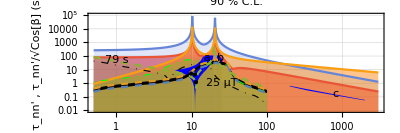

```mathematica
lineStyle={Thick,Black};
pnt3=Point[Log@{9.8,5.2}];
pnt4=Point[Log@{11,4.4}];
pnt5=Point[Log@{11.4,1.2}];
thk=.004;tfoill=0.05333333333333333;
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
LogLogPlot[
{
(*1*)ConditionalExpression[79,0<bp<25],
(*2*)ConditionalExpression[110,((14.2<bp<19.5))],
(*3*)ConditionalExpression[taubppnpi[0,bp,198,0,380,tfoill*CubeRoot[3]]-taubppnpi[20,bp,198,0,320,tfoill*CubeRoot[3]],6<bp<20],
(*4*)ConditionalExpression[-taubppnpi[0,bp,198,0,380,tfoill*CubeRoot[3]]+taubppnpi[20,bp,198,0,320,tfoill*CubeRoot[3]],((7.5<bp<19.94))],
(*5*)ConditionalExpression[taubppnpi[20,bp+5,198,0,380,tfoill*CubeRoot[3]],6<bp<14.2],
(*6*)ConditionalExpression[taubppnpi[20,bp-5,198,0,256,tfoill*CubeRoot[3]],((25.45<bp<29.5))],
(*7*)ConditionalExpression[taubppnpi[20,bp,198,0,500,tfoill*CubeRoot[3]],((20.1<bp<10000))],
(*8*)ConditionalExpression[110,((20.9<bp<25.45))],
(*9*)ConditionalExpression[taubppnpi[56,bp,198,0,480,tfoill*CubeRoot[3]*1.7],((200<bp<340))],
(*10*)ConditionalExpression[(100/bp)+.005,((340<bp<2000))],
(*11*)((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095]^4)/2)^0.25,
(*12*)((tauold[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mo1095]^4)/2+(tauold[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mo2095]^4)/2)^0.25,
(*13*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095]^4)/2)^0.25,
(*14*)ConditionalExpression[fzbe[bp],0.5<bp<100],
(*15*)ConditionalExpression[fzba[bp],0.5<bp<100],
(*16*)ConditionalExpression[fzbsignal1[bp],0.5<bp<100],
(*17*)ConditionalExpression[fzbsignal2[bp],0.5<bp<100],
(*18*)ConditionalExpression[fzbsignal3[bp],0.5<bp<100]
},{bp,.5,3000},
PlotRange->{{.5,3000},{.01,100001}},Axes->None,GridLines->Automatic,
Filling->{{1->0.001},{3->{{5},Blue}},{4->{{5},Blue}},{4->{{2},Blue}},{7->{{8},Blue}},{7->{{9},Blue}},{7->{{10},Blue}},{11->{0.001,Directive[Opacity[.45],Red]}},{12->0.001},{13->{0.001,Directive[Opacity[.45],Orange]}},{14->0.001},{15->0.001},{16->{{17},Black}},{18->0.001}},
PlotStyle->{None,None,None,None,None,None,None,None,None,None,{Automatic,Thickness[thk]},Automatic,{Automatic,Thickness[thk]},{DotDashed,Thickness[thk/2],Black},{DotDashed,Thickness[thk/2],Green},{Dashed},{Dashed},{Dashed}},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk2[-1,4,.02,0,0,0,1],tk2[-1,4,.02,0,0,0,1]},{tk2[-1,3,.02,0,0,0,1/2],tk2[-1,3,.02,0,0,0,1/2]}},FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn' , τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},PlotLegends->Join[Table["",{k,1,10}],{"(E-1)","Projection","A","ZB: (E-1)","ZB: A","AP S: <B'_⇕>_min","AP S: <B'_⇕>_max","AP S: <B'_⇔>_min"}],PlotLabel->"90 % C.L.",
Epilog->{
{Directive[{PointSize[.0075],Black}],pnt3,pnt4,pnt5},
{Directive[lineStyle],Text[Style["a",FontSize->Large],Log@{16,75}],Text[Style["b",FontSize->Large],Log@{24,75}],Text[Style["c",FontSize->Large],Log@{800,.15}],
Text[Style["79 s",FontSize->Large],Log@{1,50}],
Text[Style["25 μT",FontSize->Large],Log@{25,1}]}
},ImageSize->{1400},AspectRatio->1/3
]
```

```mathematica
mincur=FindMinimum[((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095]^4)/2)^0.25,{bp,0,10}]
Solve[((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095]^4)/2)^0.25==mincur[[1]],bp][[-1]]
```

{79.9328,{bp→2.09397×10^-9}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{bp→25.2282}

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

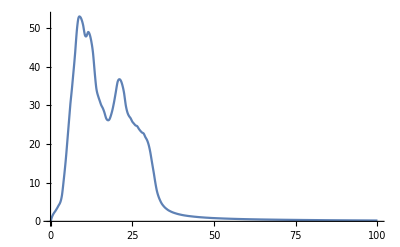

```mathematica
Plot[fzba[x],{x,0,100}]
```